```mathematica
Quit[]
```

```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/4-16-443.txt","Data"];
```

```mathematica
Dimensions[rawdata]
```

{10000,6}

```mathematica
(*blahblahblah*)
```

```mathematica
Take[rawdata,30,2]//MatrixForm
```

(Record Length | 10000
Sample Interval | 4.×10^-7
Trigger Point | 760.
 | 
 | 
 | 
Source | CH1
Vertical Units | V
Vertical Scale | 0.01
Vertical Offset | 0.0128
Horizontal Units | s
Horizontal Scale | 0.0004
Pt Fmt | Y
Yzero | 0.
Probe Atten | 10.
 | 
Note | TDS 3012 - 4:43:13 PM   4/16/2009
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | )

```mathematica
signal=Take[rawdata,All,{4,5}];
```

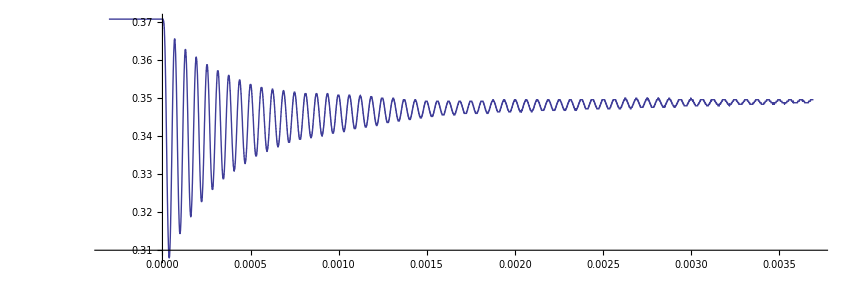

```mathematica
ListPlot[signal,PlotRange->All,PlotStyle->{PointSize[.002]},Joined->True,AspectRatio->1/3]
```

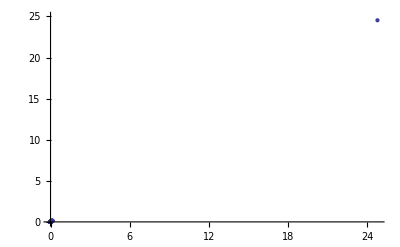

```mathematica
ListPlot[Abs[Fourier[signal]],PlotRange->{0,25}]
```